# Vaje iz Mathematice, 3. del

### 1. naloga:

Nariši graf funkcije y=a sin (k x+n), pri čemer boš lahko vrednosti parametrov a, k in n spreminjal v obsegu od -3 do 3. Območje risanja omeji na [-5,5]×[-5,5]. Enoti na x in y osi naj bosta enako veliki.

```mathematica
Manipulate[Plot[a Sin[k x+n],{x,-5,5},PlotRange->{-5,5},AspectRatio->Automatic],{{a,1},-3,3},{{k,1},-3,3},{{n,1},-3,3}]
```

### 2. naloga:

Nariši graf premice y=k x+n  in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0,y_0), pri čemer boš lahko spreminjal vrednosti parametrov k, n, x_0 in y_0. Na sliki označi z majhnim krogcem, kje leži točka T.

```mathematica
Manipulate[Plot[{k x+n,(x0-x)/k+y0},{x,-5,5},PlotRange->{-5,5},AspectRatio->Automatic,Epilog->{PointSize[Large],Point[{x0,y0}]}],{{k,1},-5,5},{{n,1},-5,5},{{x0,1},-5,5},{{y0,1},-5,5}]
```

### 3. naloga:

Definiraj funkcijo  f(x)=(x(x-2))^2/(x^2+1) ter nariši njen graf skupaj s tangento v točki x_0, tako da boš lahko spreminjal vrednost parametra x_0. Na sliki označi z majhnim krogcem, kje se tangenta dotika grafa funkcije.

```mathematica
f[x_]=(x (x-2))^2/(x^2+1);
Manipulate[
Plot[
{ f[x],
f'[x0] (x-x0)+f[x0]
},
{x,-3,3},
PlotRange->{-3,3},
Epilog->{PointSize[Large],Point[{x0,f[x0]}]}
],
{{x0,1},-5,5}
]
```

### 4. naloga:

Definiraj funkcijo  g(x)=-x^3+8  in nariši njen graf nad intervalom [-3,3].

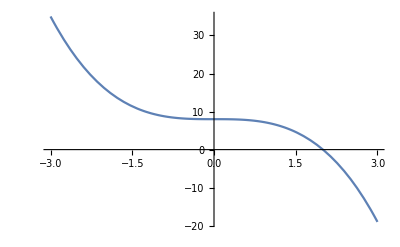

```mathematica
g[x_]=-x^3+8;
plot=Plot[g[x],{x,-3,3}]
```

Izračunaj ničlo funkcije g.

```mathematica
nicla=First[Solve[g[x]==0,Reals]];
x/.nicla
```

2

Izračunaj ploščino lika, ki ga (v prvem kvadrantu) omejujeta koordinatni osi in graf te funkcije.

```mathematica
∫_0^(x/.nicla) g[x]ⅆx
```

12

Še enkrat nariši graf funkcije g nad istim intervalom, le da bo tokrat območje, katerega ploščino si izračunal, pobarvano.

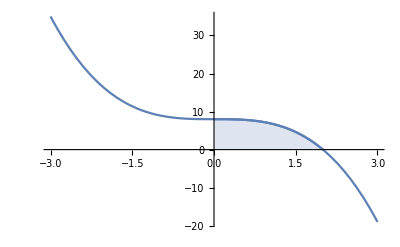

```mathematica
Show[plot,Plot[g[x],{x,0,x/.nicla},Filling->Axis]]
```

### 5. naloga:

Definiraj funkciji  h(x)=x^2-8  in  k(x)=-x^2+10  ter nariši njuna grafa.

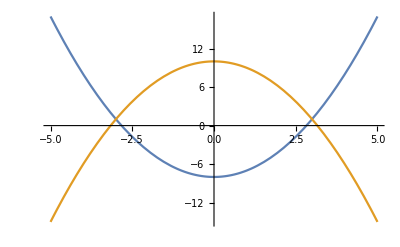

```mathematica
h[x_]=x^2-8;
k[x_]=-x^2+10;
hkplot=Plot[{h[x],k[x]},{x,-5,5}]
```

Poišči njuni presečišči.

```mathematica
nicle=x/.Solve[h[x]==k[x],x,Reals]
```

{-3,3}

Izračunaj ploščino lika, ki ga omejujeta grafa teh dveh funkcij.

```mathematica
∫_nicle⟦1⟧^nicle⟦2⟧ (h[x]-k[x])ⅆx
```

-72

Še enkrat nariši grafa obeh funkcij, le da bo tokrat območje, katerega ploščino si izračunal, pobarvano.

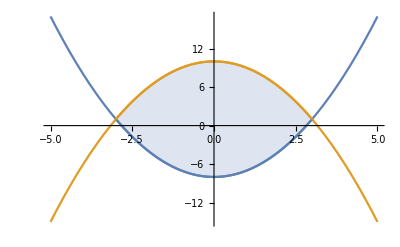

```mathematica
Show[hkplot,Plot[{h[x],k[x]},{x,nicle⟦1⟧,nicle⟦2⟧},Filling->{1->{2}}]]
```

### 6. naloga:

Nariši graf funkcije u(x)=x^3-8 x^2+100  na intervalu [-5,10] in pobarvaj površino med grafom in vodoravno osjo na intervalu [a,b], kjer lahko parametra a in b spreminjaš od -5 do 10. Začetna vrednost parametra a naj bo 1, začetna vrednost parametra b pa 8. Nariši še navpični črti med vodoravno osjo in grafom v točkah x=a  in  x=b. Črti naj bosta enake barve kot graf funkcije.

```mathematica
u[x_]=x^3-8 x^2+100;
Manipulate[Show[Plot[u[x],{x,-5,10},PlotStyle->Blue,Epilog->{Blue,Line[{{a,0},{a,u[a]}}],Line[{{b,0},{b,u[b]}}]}],Plot[u[x],{x,a,b},PlotStyle->Blue,Filling->Axis,AxesOrigin->{0,0}]],{{a,1},-5,10},{{b,8},-5,10}]
```

### 7. naloga:

Nariši graf, ki prikazuje, kako se funkcije  f_n(x)=(1+x/n)^n  približujejo svoji limiti  g(x)=ⅇ^x. Graf naj prikazuje funkcije f_1,f_2, ...,f_10 (vse enake barve) in funkcijo g (drugačne barve). Sam izberi primeren interval.

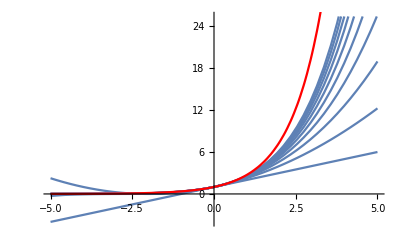

```mathematica
Show[Plot[{(1+x/n)^n/.n->Range[10]},{x,-5,5}],Plot[ⅇ^x,{x,-5,5},PlotStyle->Red]]
```

### 8. naloga:

Definiraj funkcijo, ki sprejme naravno število in vrne njegovo število različnih prafaktorjev.

Poišči vsa tista števila med 1 in 1000, ki imajo največje število različnih prafaktorjev. Namig: oglej si funkcijo MaximalBy.

```mathematica
nfaktorjev[x_]:=Length[FactorInteger[x]]
MaximalBy[Range[1000],nfaktorjev]
```

{210,330,390,420,462,510,546,570,630,660,690,714,770,780,798,840,858,870,910,924,930,966,990}

### 9. naloga:

Tabeliraj numerične vrednosti funkcije  sin (2x)√x v točkah 0, π/12,π/6,π/4,π/3,(5π)/12,π/2.

```mathematica
li=Table[N[Sin[2 x] √x],{x,Table[(n π)/12,{n,0,6}]}];
li//TableForm
```

0.
0.255832
0.626657
0.886227
0.886227
0.572057
0.

Katera od dobljenih vrednosti je najbližja številu 1/3? Namig: uporabiš lahko funkcijo MinimalBy.

```mathematica
MinimalBy[li,Abs[#-1/3]&]
```

{0.255832}

### 10. naloga:

Definiraj funkcijo  f(x)=sin (3x)+x^2-5  in nariši njen graf na intervalu [-3,3].

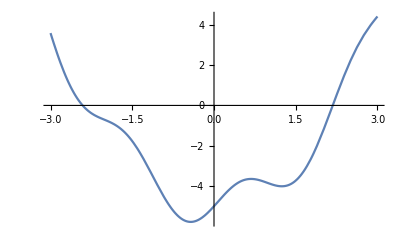

```mathematica
f10[x_]=Sin[3 x]+x^2-5;
fplot=Plot[f10[x],{x,-3,3}]
```

Z numeričnim reševanjem enačb (FindRoot) poišči ničli funkcije f

```mathematica
nicle=x/.{FindRoot[f10[x]==0,{x,5}],FindRoot[f10[x]==0,{x,-4}]}
```

{2.17912,-2.41113}

Izračunaj ploščino med grafom funkcije in vodoravno osjo na intervalu med ničlama.

```mathematica
∫_nicle⟦1⟧^nicle⟦2⟧ f10[x]ⅆx
```

14.9584

Še enkrat nariši graf funkcije in pri tem pobarvaj območje, katerega ploščino si izračunal.

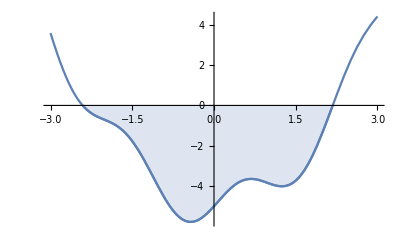

```mathematica
Show[fplot,Plot[f10[x],{x,nicle⟦1⟧,nicle⟦2⟧},Filling->Axis]]
```

### 11. naloga:

Praštevilski dvojček sta taki praštevili p in q, da velja q=p+2. Na primer, števili 71 in 73 tvorita praštevilški dvojček. Katera izmed prvih 100 praštevil nastopajo v praštevilskem dvojčku? Sestavi seznam, ki jih vsebuje.

```mathematica
Select[Table[Prime[n],{n,100}],PrimeQ[#1+2]||PrimeQ[#1-2]&]
```

{3,5,7,11,13,17,19,29,31,41,43,59,61,71,73,101,103,107,109,137,139,149,151,179,181,191,193,197,199,227,229,239,241,269,271,281,283,311,313,347,349,419,421,431,433,461,463,521,523}

Sestavi seznam praštevilskih dvojčkov, pri čemer je manjše število v dvojčku eno od prvih 100 praštevil.

### 12. naloga:

Izračunaj  (3001
576).

```mathematica
a=Binomial[3001,576]
```

410048707006040685442610275632592427326759475520581519245144080792862726417564262314683565253901947155760471315360734919735315360018593893106242809167489839149170232630515009496094158211307757223248372896120994102148675618437798957338576183073449720800393068687557245809524395258681218807876001532406292169343967369683305663516881554634680427814450759552826925246371932629229403794926164921540466004177410799901673525189417223510313419120521596855390653037035207492728643442211760608907069135485685321568236496210654513330701757195056039675914922120074112297384444857272372346058669265639356380774878289648168848751825279669756026736450

Razcepi dobljeno vrednost.

```mathematica
faktorji=FactorInteger[a]
```

{{2,1},{3,4},{5,2},{7,1},{11,1},{17,2},{19,1},{29,2},{31,1},{37,2},{53,2},{61,1},{73,1},{83,1},{103,1},{107,1},{149,1},{157,1},{163,1},{193,1},{197,1},{199,1},{211,1},{223,1},{227,1},{229,1},{271,1},{293,1},{307,1},{311,1},{313,1},{317,1},{331,1},{347,1},{349,1},{353,1},{359,1},{367,1},{373,1},{409,1},{419,1},{421,1},{487,1},{491,1},{499,1},{577,1},{587,1},{593,1},{599,1},{607,1},{613,1},{617,1},{619,1},{631,1},{641,1},{643,1},{647,1},{653,1},{659,1},{661,1},{673,1},{677,1},{683,1},{691,1},{701,1},{709,1},{719,1},{727,1},{733,1},{739,1},{743,1},{809,1},{811,1},{821,1},{823,1},{827,1},{829,1},{839,1},{853,1},{857,1},{859,1},{863,1},{877,1},{881,1},{883,1},{887,1},{907,1},{911,1},{919,1},{929,1},{937,1},{941,1},{947,1},{953,1},{967,1},{971,1},{977,1},{983,1},{991,1},{997,1},{1213,1},{1217,1},{1223,1},{1229,1},{1231,1},{1237,1},{1249,1},{1259,1},{1277,1},{1279,1},{1283,1},{1289,1},{1291,1},{1297,1},{1301,1},{1303,1},{1307,1},{1319,1},{1321,1},{1327,1},{1361,1},{1367,1},{1373,1},{1381,1},{1399,1},{1409,1},{1423,1},{1427,1},{1429,1},{1433,1},{1439,1},{1447,1},{1451,1},{1453,1},{1459,1},{1471,1},{1481,1},{1483,1},{1487,1},{1489,1},{1493,1},{1499,1},{2437,1},{2441,1},{2447,1},{2459,1},{2467,1},{2473,1},{2477,1},{2503,1},{2521,1},{2531,1},{2539,1},{2543,1},{2549,1},{2551,1},{2557,1},{2579,1},{2591,1},{2593,1},{2609,1},{2617,1},{2621,1},{2633,1},{2647,1},{2657,1},{2659,1},{2663,1},{2671,1},{2677,1},{2683,1},{2687,1},{2689,1},{2693,1},{2699,1},{2707,1},{2711,1},{2713,1},{2719,1},{2729,1},{2731,1},{2741,1},{2749,1},{2753,1},{2767,1},{2777,1},{2789,1},{2791,1},{2797,1},{2801,1},{2803,1},{2819,1},{2833,1},{2837,1},{2843,1},{2851,1},{2857,1},{2861,1},{2879,1},{2887,1},{2897,1},{2903,1},{2909,1},{2917,1},{2927,1},{2939,1},{2953,1},{2957,1},{2963,1},{2969,1},{2971,1},{2999,1},{3001,1}}

Izmed vseh prafaktorjev izberi tiste, ki se v razcepu števila pojavijo več kot enkrat.

```mathematica
Table[First[f],{f,Select[faktorji,Last[#1]>1&]}]
```

{3,5,17,29,37,53}

S pomočjo faktorizacije dokaži, da je  ∑_(k=0)^10 (10
k)x^k=(x+1)^10

```mathematica
Factor[∑_(k=0)^10 Binomial[10,k] x^k]==Factor[(x+1)^10]
```

True

### 13. naloga:

Nariši graf implicitno podane funkcije  y^2-y-2=(x^2-1)^3  na območju [-5,5]×[-5,5].

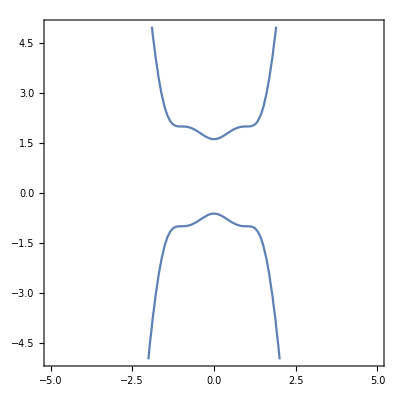

```mathematica
ContourPlot[y^2-y-2==(x^2-1)^3,{x,-5,5},{y,-5,5},Axes->True]
```

Poišči ekplicitno obliko funkcije  y=f(x)  pri pogoju y≥0. Se pravi, definiraj funkcijo f, da bo veljalo f(x)≥0 in (f(x))^2-f(x)-2=(x^2-1)^3 za vse x.

```mathematica
f13[x]=y/.First@@Solve[y^2-y-2==(x^2-1)^3&&y≥0,y,Reals]
```

1/2+1/2 √(5+12 x^2-12 x^4+4 x^6)

Preveri, ali res velja  (f(x))^2-f(x)-2=(x^2-1)^3

```mathematica
f13[x]^2-f13[x]-2==(x^2-1)^3//Simplify
```

True

Nariši graf funkcije f na [-2,2]×[0,5]. Enoti na oseh naj bosta enaki.

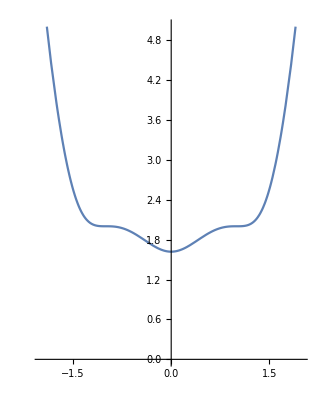

```mathematica
Plot[f13[x],{x,-2,2},PlotRange->{{-2,2},{0,5}},AspectRatio->Automatic]
```

### 14. naloga:

Nariši graf implicitno podane funkcije  |x|^(2/3)+|y|^(2/3)=1  na območju [-1,1]×[-1,1]

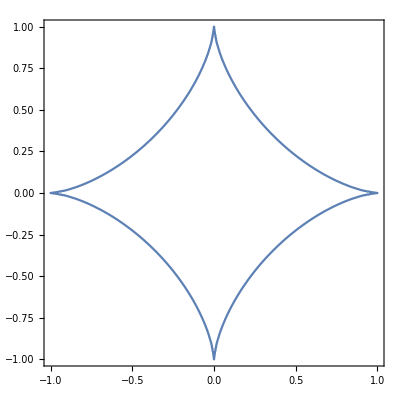

```mathematica
ContourPlot[Abs[x]^(2/3)+Abs[y]^(2/3)==1,{x,-1,1},{y,-1,1}]
```

Prikaži, kako se spreminja graf implicitne krivulje  |x|^p+|y|^p=1  za vrednosti parametra p∈[0,4]  z začetno vrednostjo 2.

```mathematica
Manipulate[ContourPlot[Abs[x]^p+Abs[y]^p==1,{x,-1,1},{y,-1,1}],{{p,2},0,4}]
```

Pri kateri vrednosti p leži točka (1/3,1/3) na grafu krivulje?

```mathematica
p/.First@@Solve[Abs[1/3]^p+Abs[1/3]^p==1,p,Reals]
```

Log[2]/Log[3]

### 15. naloga:

Naj bo p(x)=a x^2+b x+c. Za nekatere vrednosti koeficientov a, b, c se zaporedje p(1), p(2), p(3),... začne s praštevili. Na primer, če je p(x)=x^2+3x+1, dobimo zaporedje, katerega prvih pet členov so praštevila. Poiščimo take vrednosti 1≤a, b, c≤25, da bodo p(1),p(2),p(3),...,p(15) praštevila. Do rešitve pridemo v naslednjih korakih:

Definiraj funkcijo, ki sprejme seznam koeficientov a,b,c in vrne True, če so vrednosti polinoma a x^2+b x+c praštevila za vsa naravna števila 1≤x≤15. Namig: kaj naredi Apply[And,seznam]?

```mathematica
firstPrimeQ[a_,b_,c_]:=Length[Select[Table[a x^2+b x+c,{x,1,15}],PrimeQ]]==15
```

Sestavi seznam vseh možnih trojic števil {a,b,c}, kjer velja 1≤a,b,c≤25.

```mathematica
trojice=Tuples[Range[25],3]
```

{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,1,10},{1,1,11},{1,1,12},{1,1,13},{1,1,14},{1,1,15},{1,1,16},{1,1,17},{1,1,18},{1,1,19},{1,1,20},{1,1,21},{1,1,22},15582,{25,25,5},{25,25,6},{25,25,7},{25,25,8},{25,25,9},{25,25,10},{25,25,11},{25,25,12},{25,25,13},{25,25,14},{25,25,15},{25,25,16},{25,25,17},{25,25,18},{25,25,19},{25,25,20},{25,25,21},{25,25,22},{25,25,23},{25,25,24},{25,25,25}}
 |  |  |  |

Iz seznama vseh trojic izberi tiste, ki določajo zaporedje, ki ima na začetku vsaj 15 praštevil.

```mathematica
Select[trojice,Function[consts,firstPrimeQ@@consts]]
```

{{1,1,17},{1,21,1},{1,23,23},{2,2,19},{2,6,23},{3,3,23},{6,12,23},{7,7,17}}